#### Heap Linear Layer

```mathematica
Block[{L=8,a=0.5,h=4,h2=2.5,d,nd,nds,map,hl,tree},
d=Ceiling[Log[2,L]]+1;
nd[i_]:={Rectangle[{-a,-a},{a,a},RoundingRadius->0.1a],{Black,Text[StringTemplate["\!\(x\_`1`\)"][i],{0,0}]}};
nds={EdgeForm[Directive[AbsoluteThickness[1],GrayLevel[0.6]]],Table[{Lighter[ColorData[0][l],0.95-0.05l],Table[Translate[nd[i],{i,0}],{i,Floor[2^(l-1)],2^l-1}]},{l,0,d-1}]};
map[i_,j_]:=Arrow[BSplineCurve[{{i,a},{i,2a},{(i+j)/2,h/2},{j,h-2a},{j,h-a}}]];
hl[k0_]:={Arrowheads[{{0.01,0.9,Graphics[Line[Offset/@{{-4,2},{0,0},{-4,-2}}]]}}],
Table[{ColorData[0][k],Opacity[0.6],
Table[Block[{i0,i1},
i0=Floor[2^(l-1)];
i1=2^l;
Table[Block[{j0,j1},
If[i==0,
j0=Floor[2^(k-1)];
j1=Floor[2^(k-1)]+Ceiling[2^(k-1)],
j0=i 2^k;
j1=(i+1) 2^k];
Table[If[j1≤L,map[i,j],Nothing],
{j,j0,j1-1}]],{i,i0,i1-1}]],
{l,0,d-1}]},
{k,k0,d-1}]};
tree={{Arrowheads[{{0.01,0.5,Graphics[Line[Offset/@{{-4,2},{0,0},{-4,-2}}]]}}],Table[{Table[Translate[Table[Arrow[{{0,0},{2^(d-l-1)(q-1/2),-h2}}],{q,If[l==0,{1/2},{0,1}]}],{2^(d-l)(i-2^(l-1)+FractionalPart[2^(l-1)]/2+1/2),-h2 l}],{i,Floor[2^(l-1)],2^l-1}]},{l,0,d-2}]},{EdgeForm[Directive[AbsoluteThickness[1],GrayLevel[0.6]]],Table[{Lighter[ColorData[0][l],0.95-0.05l],Table[Translate[nd[i],{2^(d-l)(i-2^(l-1)+FractionalPart[2^(l-1)]/2+1/2),-h2 l}],{i,Floor[2^(l-1)],2^l-1}]},{l,0,d-1}]}};
Graphics[{Translate[#1,{0,#2h}]&@@@Thread@{{hl[1],hl[0]},{0,1}},
Translate[nds,{0,# h}]&/@Range[0,2],Text["(b)",{-1.2,8}],
Translate[{tree,Text["(a)",{1,0.5}]},{-9,7.5}]},ImageSize->260]]
```

-Graphics-

```mathematica
Block[{L=8,a=0.5,h=4,h2=2.5,d,nd,nds,map,hl,tree},
d=Ceiling[Log[2,L]]+1;
nd[i_,l_]:={Lighter[ColorData[0][l],0.95-0.05l],Rectangle[{-a,-a},{a,a},RoundingRadius->0.1a],{Black,Text[StringTemplate["\!\(z\_`1`\)"][i],{0,0}]}};
nds={EdgeForm[Directive[AbsoluteThickness[1],GrayLevel[0.6]]],Table[{Table[Translate[nd[i,l],{i,0}],{i,Floor[2^(l-1)],2^l-1}]},{l,0,d-1}]};
map[i_,j_]:=Arrow[BSplineCurve[{{i,a},{i,2a},{(i+j)/2,h/2},{j,h-2a},{j,h-a}}]];
hl[k0_]:={Arrowheads[{{0.01,0.78,Graphics[Line[Offset/@{{-4,2},{0,0},{-4,-2}}]]}}],
Opacity[0.8],AbsoluteThickness[1.5],
Table[
Table[Block[{i0,i1},
i0=Floor[2^(l-1)];
i1=2^l;
Table[Block[{j0,j1},
j0=i 2^k;
j1=(i+1) 2^k;
Table[If[j1≤L,{If[k==0,GrayLevel[0.6],
ColorData[0][2l+(j-i 2^k)-1]],map[i,j]},Nothing],
{j,j0,j1-1}]],{i,i0,i1-1}]],
{l,1,d-1}],
{k,k0,1(*d-1*)}]};
tree={{Arrowheads[{{0.01,0.5,Graphics[Line[Offset/@{{-4,2},{0,0},{-4,-2}}]]}}],
Opacity[0.8],AbsoluteThickness[1.5],Table[{Table[Translate[Table[{ColorData[0][Mod[2l+q-1,5]],Arrow[{{0,0},{2^(d-l-1)(q-1/2),-h2}}]},{q,{0,1}}],{2^(d-l)(i-2^(l-1)+FractionalPart[2^(l-1)]/2+1/2),-h2 l}],{i,Floor[2^(l-1)],2^l-1}]},{l,1,d-2}]},{EdgeForm[Directive[AbsoluteThickness[1],GrayLevel[0.6]]],Table[{Table[Translate[nd[i,l],{2^(d-l)(i-2^(l-1)+FractionalPart[2^(l-1)]/2+1/2),-h2 l}],{i,Floor[2^(l-1)],2^l-1}]},{l,0,d-1}]}};
Graphics[{Translate[#1,{0,#2h}]&@@@Thread@{{hl[1],hl[0]},{0,1}},
Translate[nds,{0,# h}]&/@Range[0,2],Text["(b)",{-1.2,8}],
Translate[{tree,Text["(a)",{1,0.5}]},{-9,7.5}]},ImageSize->260]]
```

-Graphics-

#### Test Scoping

```mathematica
Block[{n=4,d=2,p},
p[rng_,dim_,ind_]:=
If[EvenQ@Total@rng⟦dim+1⟧,
Block[{mid=Total@rng⟦dim+1⟧/2,rng1,rng2},
rng1=rng;rng2=rng;
rng1⟦dim+1,2⟧=mid;
rng2⟦dim+1,1⟧=mid;
Sow[ind->rng1,1];
Sow[ind->rng2,2];
p[rng1,Mod[dim+1,d],2 ind];
p[rng2,Mod[dim+1,d],2 ind+1];
]];
Reap[p[ConstantArray[{0,n},d],0,1]]]
```

{Null,{{1→{{0,2},{0,4}},2→{{0,2},{0,2}},4→{{0,1},{0,2}},8→{{0,1},{0,1}},9→{{1,2},{0,1}},5→{{0,1},{2,4}},10→{{0,1},{2,3}},11→{{1,2},{2,3}},3→{{2,4},{0,2}},6→{{2,3},{0,2}},12→{{2,3},{0,1}},13→{{3,4},{0,1}},7→{{2,3},{2,4}},14→{{2,3},{2,3}},15→{{3,4},{2,3}}},{1→{{2,4},{0,4}},2→{{0,2},{2,4}},4→{{1,2},{0,2}},8→{{0,1},{1,2}},9→{{1,2},{1,2}},5→{{1,2},{2,4}},10→{{0,1},{3,4}},11→{{1,2},{3,4}},3→{{2,4},{2,4}},6→{{3,4},{0,2}},12→{{2,3},{1,2}},13→{{3,4},{1,2}},7→{{3,4},{2,4}},14→{{2,3},{3,4}},15→{{3,4},{3,4}}}}}

#### S3 group multiplication table

```mathematica
TableForm[GroupMultiplicationTable[SymmetricGroup[3]]-1,TableHeadings->{Range[0,5],Range[0,5]}]
```

| 0 | 1 | 2 | 3 | 4 | 5
0 | 0 | 1 | 2 | 3 | 4 | 5
1 | 1 | 0 | 3 | 2 | 5 | 4
2 | 2 | 4 | 0 | 5 | 1 | 3
3 | 3 | 5 | 1 | 4 | 0 | 2
4 | 4 | 2 | 5 | 0 | 3 | 1
5 | 5 | 3 | 4 | 1 | 2 | 0

```mathematica
GroupElements[SymmetricGroup[3]]
```

{Cycles[{}],Cycles[{{2,3}}],Cycles[{{1,2}}],Cycles[{{1,2,3}}],Cycles[{{1,3,2}}],Cycles[{{1,3}}]}

```mathematica
StringDelete["[[0, 1, 2, 3, 4, 5], [1, 0, 3, 2, 5, 4], [2, 4, 0, 5, 1, 3], [3, 5, 1,
   4, 0, 2], [4, 2, 5, 0, 3, 1], [5, 3, 4, 1, 2, 0]]"," "]
```

[[0,1,2,3,4,5],[1,0,3,2,5,4],[2,4,0,5,1,3],[3,5,1,
4,0,2],[4,2,5,0,3,1],[5,3,4,1,2,0]]

#### Free Energy Benchmark

```mathematica
Block[{L=2,J=0.1,xs,eng},
xs=ArrayReshape[Tuples[{-1,1},L^2],{2^(L^2),L,L}];
eng[x_]:=-J Total@Flatten[x.RotateLeft[x,{1,0}]+x.RotateLeft[x,{0,1}]];
-Log@Total@Exp[-eng/@xs]]
```

-3.3265

```mathematica
Block[{L=2,J=0.1,xs,eng,es,ps},
xs=ArrayReshape[Tuples[{-1,1},L^2],{2^(L^2),L,L}];
eng[x_]:=-J Total@Flatten[x.RotateLeft[x,{1,0}]+x.RotateLeft[x,{0,1}]];
es=eng/@xs;
ps=#/Total[#]&@Exp[-es];
Column@Thread[Range[0,Length@ps-1]->ps]]
```

0→0.177906
1→0.0535844
2→0.0535844
3→0.0359187
4→0.0535844
5→0.0359187
6→0.0359187
7→0.0535844
8→0.0535844
9→0.0359187
10→0.0359187
11→0.0535844
12→0.0359187
13→0.0535844
14→0.0535844
15→0.177906

#### 2D Fractal

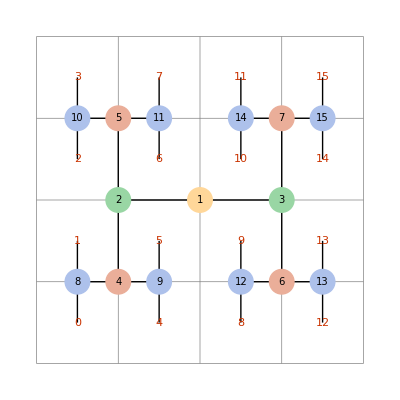

```mathematica
Block[{n=4,d=2,p},
p[rng_,dim_,ind_]:=
If[EvenQ@Total@rng⟦dim+1⟧,
Block[{mid=Total@rng⟦dim+1⟧/2,rng1,rng2,p1,p2},
rng1=rng;rng2=rng;
rng1⟦dim+1,2⟧=mid;
rng2⟦dim+1,1⟧=mid;
p1=p[rng1,Mod[dim+1,d],2 ind];
p2=p[rng2,Mod[dim+1,d],2 ind+1];
{{Line[{Mean/@rng,Mean/@rng1}],p1},{Line[{Mean/@rng,Mean/@rng2}],p2},
Translate[{{EdgeForm[AbsoluteThickness[1]],Lighter[ColorData[0,Log[2,Times@@(Subtract@@@rng)]],0.6],Disk[{0,0},0.15]},Text[Style[ind,10],{0,0}]},Mean/@rng]}],
{Red,Translate[Text[#.n^Range[d-1,0,-1]],#+{1,1}/2]&@rng⟦;;,1⟧}];
Graphics[{{Gray,AbsoluteThickness[0.5],Line[{{#,0},{#,n}}&/@Range[0,n]],Line[{{0,#},{n,#}}&/@Range[0,n]]},{p[ConstantArray[{0,n},d],0,1]}}]]
```

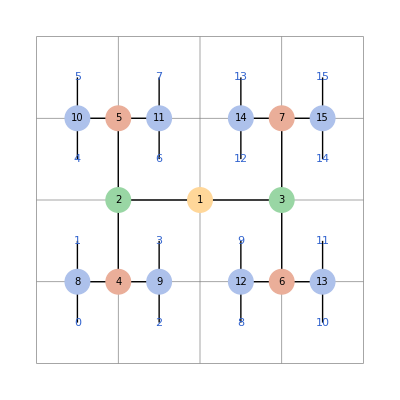

```mathematica
Block[{n=4,d=2,p},
p[rng_,dim_,ind_]:=
If[EvenQ@Total@rng⟦dim+1⟧,
Block[{mid=Total@rng⟦dim+1⟧/2,rng1,rng2,p1,p2},
rng1=rng;rng2=rng;
rng1⟦dim+1,2⟧=mid;
rng2⟦dim+1,1⟧=mid;
p1=p[rng1,Mod[dim+1,d],2 ind];
p2=p[rng2,Mod[dim+1,d],2 ind+1];
{{Line[{Mean/@rng,Mean/@rng1}],p1},{Line[{Mean/@rng,Mean/@rng2}],p2},
Translate[{{EdgeForm[AbsoluteThickness[1]],Lighter[ColorData[0,Log[2,Times@@(Subtract@@@rng)]],0.6],Disk[{0,0},0.15]},Text[Style[ind,10],{0,0}]},Mean/@rng]}],
{Blue,Translate[Text[ind-n^d],#+{1,1}/2]&@rng⟦;;,1⟧}];
Graphics[{{Gray,AbsoluteThickness[0.5],Line[{{#,0},{#,n}}&/@Range[0,n]],Line[{{0,#},{n,#}}&/@Range[0,n]]},{p[ConstantArray[{0,n},d],0,1]}}]]
```

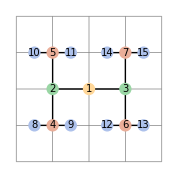

```mathematica
Block[{n=4,d=2,p},
p[rng_,dim_,ind_]:=
If[EvenQ@Total@rng⟦dim+1⟧,
Block[{mid=Total@rng⟦dim+1⟧/2,rng1,rng2,p1,p2},
rng1=rng;rng2=rng;
rng1⟦dim+1,2⟧=mid;
rng2⟦dim+1,1⟧=mid;
p1=p[rng1,Mod[dim+1,d],2 ind];
p2=p[rng2,Mod[dim+1,d],2 ind+1];
{If[p1=!={},{Line[{Mean/@rng,Mean/@rng1}],p1},Nothing],If[p2=!={},{Line[{Mean/@rng,Mean/@rng2}],p2},Nothing],
Translate[{{EdgeForm[AbsoluteThickness[1]],Lighter[ColorData[0,Log[2,Times@@(Subtract@@@rng)]],0.6],Disk[{0,0},0.15]},Text[Style[ind,10],{0,0}]},Mean/@rng]}],
{}];
Graphics[{{Gray,AbsoluteThickness[0.5],Line[{{#,0},{#,n}}&/@Range[0,n]],Line[{{0,#},{n,#}}&/@Range[0,n]]},{p[ConstantArray[{0,n},d],0,1]}}]]
```

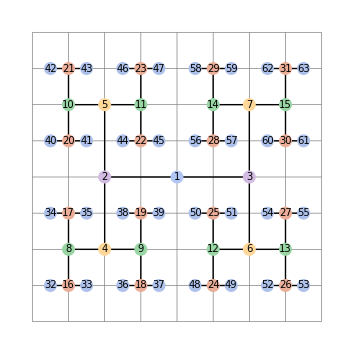

```mathematica
Block[{n=8,d=2,p},
p[rng_,dim_,ind_]:=
If[EvenQ@Total@rng⟦dim+1⟧,
Block[{mid=Total@rng⟦dim+1⟧/2,rng1,rng2,p1,p2},
rng1=rng;rng2=rng;
rng1⟦dim+1,2⟧=mid;
rng2⟦dim+1,1⟧=mid;
p1=p[rng1,Mod[dim+1,d],2 ind];
p2=p[rng2,Mod[dim+1,d],2 ind+1];
{If[p1=!={},{Line[{Mean/@rng,Mean/@rng1}],p1},Nothing],If[p2=!={},{Line[{Mean/@rng,Mean/@rng2}],p2},Nothing],
Translate[{{EdgeForm[AbsoluteThickness[1]],Lighter[ColorData[0,Log[2,Times@@(Subtract@@@rng)]],0.6],Disk[{0,0},0.16]},Text[Style[ind,10],{0,0}]},Mean/@rng]}],
{}];
Graphics[{{Gray,AbsoluteThickness[0.5],Line[{{#,0},{#,n}}&/@Range[0,n]],Line[{{0,#},{n,#}}&/@Range[0,n]]},{p[ConstantArray[{0,n},d],0,1]}}]]
```

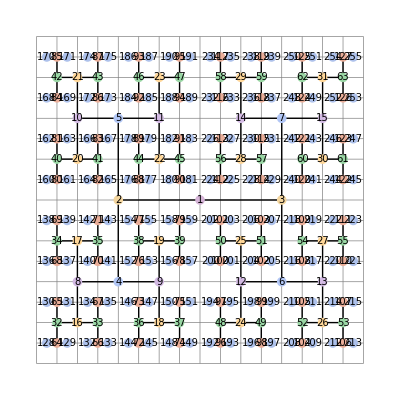

```mathematica
Block[{n=16,d=2,p},
p[rng_,dim_,ind_]:=
If[EvenQ@Total@rng⟦dim+1⟧,
Block[{mid=Total@rng⟦dim+1⟧/2,rng1,rng2,p1,p2},
rng1=rng;rng2=rng;
rng1⟦dim+1,2⟧=mid;
rng2⟦dim+1,1⟧=mid;
p1=p[rng1,Mod[dim+1,d],2 ind];
p2=p[rng2,Mod[dim+1,d],2 ind+1];
{If[p1=!={},{Line[{Mean/@rng,Mean/@rng1}],p1},Nothing],If[p2=!={},{Line[{Mean/@rng,Mean/@rng2}],p2},Nothing],
Translate[{{EdgeForm[AbsoluteThickness[1]],Lighter[ColorData[0,Log[2,Times@@(Subtract@@@rng)]],0.6],Disk[{0,0},0.2]},Text[Style[ind,10],{0,0}]},Mean/@rng]}],
{}];
Graphics[{{Gray,AbsoluteThickness[0.5],Line[{{#,0},{#,n}}&/@Range[0,n]],Line[{{0,#},{n,#}}&/@Range[0,n]]},{p[ConstantArray[{0,n},d],0,1]}}]]
```

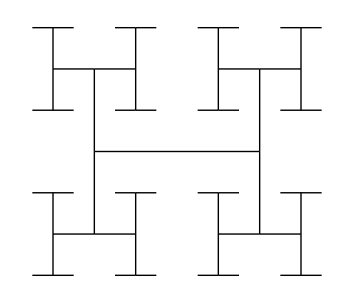

```mathematica
Block[{n=8,d=2,p},
p[rng_,dim_,ind_]:=
If[EvenQ@Total@rng⟦dim+1⟧,
Block[{mid=Total@rng⟦dim+1⟧/2,rng1,rng2,p1,p2},
rng1=rng;rng2=rng;
rng1⟦dim+1,2⟧=mid;
rng2⟦dim+1,1⟧=mid;
p1=p[rng1,Mod[dim+1,d],2 ind];
p2=p[rng2,Mod[dim+1,d],2 ind+1];
{If[p1=!={},{Line[{Mean/@rng,Mean/@rng1}],p1},Nothing],If[p2=!={},{Line[{Mean/@rng,Mean/@rng2}],p2},Nothing],{}}],
{}];
Graphics[{p[ConstantArray[{0,n},d],0,1]}]]
```

```mathematica
Block[{gs},
gs=Subscript[g,#]&/@Range[0,15];
Do[Do[{gs⟦2q+1⟧=gs⟦q+1⟧,gs⟦2q+2⟧=gs⟦2^(z-1)+q+1⟧∘gs⟦q+1⟧},{q,0,2^(z-1)-1}],{z,1,1}];
gs]
```

{g_0,g_1∘g_0,g_2,g_3,g_4,g_5,g_6,g_7,g_8,g_9,g_10,g_11,g_12,g_13,g_14,g_15}

```mathematica
Block[{gs},
gs=Subscript[g,#]&/@Range[0,15];
Do[Do[{gs⟦2q+1⟧=gs⟦q+1⟧,gs⟦2q+2⟧=gs⟦2^(z-1)+q+1⟧∘gs⟦q+1⟧},{q,0,2^(z-1)-1}],{z,1,2}];
gs]
```

{g_0,g_2∘g_0,g_2∘g_0,g_3∘(g_2∘g_0),g_4,g_5,g_6,g_7,g_8,g_9,g_10,g_11,g_12,g_13,g_14,g_15}

```mathematica
Block[{gs,ζ,z=1,fs},
gs=Subscript[g,#]&/@Range[0,15];
fs=gs;
ζ=Log[2,Length@gs]+1;
Table[Do[fs⟦q+1⟧=gs⟦2q+1⟧;fs⟦2^(ζ-1-z)+q+1⟧=gs⟦2q+1⟧^(-1)gs⟦2q+2⟧;,{q,0,2^(ζ-1-z)-1}];gs=fs,{z,1,ζ-1}]]
```

{{g_0,g_2,g_4,g_6,g_8,g_10,g_12,g_14,g_1/g_0,g_3/g_2,g_5/g_4,g_7/g_6,g_9/g_8,g_11/g_10,g_13/g_12,g_15/g_14},{g_0,g_4,g_8,g_12,g_2/g_0,g_6/g_4,g_10/g_8,g_14/g_12,g_1/g_0,g_3/g_2,g_5/g_4,g_7/g_6,g_9/g_8,g_11/g_10,g_13/g_12,g_15/g_14},{g_0,g_8,g_4/g_0,g_12/g_8,g_2/g_0,g_6/g_4,g_10/g_8,g_14/g_12,g_1/g_0,g_3/g_2,g_5/g_4,g_7/g_6,g_9/g_8,g_11/g_10,g_13/g_12,g_15/g_14},{g_0,g_8/g_0,g_4/g_0,g_12/g_8,g_2/g_0,g_6/g_4,g_10/g_8,g_14/g_12,g_1/g_0,g_3/g_2,g_5/g_4,g_7/g_6,g_9/g_8,g_11/g_10,g_13/g_12,g_15/g_14}}

```mathematica
Block[{ζ=5},
Table[Table[2^(z-1)+q-> 2^(ζ-1-z){2q+1,2q+2},{q,0,2^(z-1)-1}],{z,1,ζ-1}]]
```

{{1→{8,16}},{2→{4,8},3→{12,16}},{4→{2,4},5→{6,8},6→{10,12},7→{14,16}},{8→{1,2},9→{3,4},10→{5,6},11→{7,8},12→{9,10},13→{11,12},14→{13,14},15→{15,16}}}

```mathematica
Block[{gs,ζ,z=1},
gs=Subscript[g,#]&/@Range[0,15];
ζ=Log[2,Length@gs]+1;
Table[gs =Normal@SparseArray[Flatten@Table[{{q+1}->gs⟦2q+1⟧,{2^(ζ-1-z)+q+1}->gs⟦2q+1⟧^(-1)gs⟦2q+2⟧},{q,0,2^(ζ-1-z)-1}],16],{z,1,2}]]
```

{{g_0,g_2,g_4,g_6,g_8,g_10,g_12,g_14,g_1/g_0,g_3/g_2,g_5/g_4,g_7/g_6,g_9/g_8,g_11/g_10,g_13/g_12,g_15/g_14},{g_0,g_4,g_8,g_12,g_2/g_0,g_6/g_4,g_10/g_8,g_14/g_12,0,0,0,0,0,0,0,0}}

```mathematica
SparseArray[{1->1}]
```

SparseArray[…]

```mathematica
List@@SparseArray[{1->1,2->1},{16}]
```

{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}